```mathematica
c3=I/Sqrt[3]({{0, -1, 1}, {1, 0, -1}, {-1, 1, 0}});
```

```mathematica
Eigenvalues[c3]
```

{-1,1,0}

```mathematica
T=({{1, 1, 1}, {1, Exp[2π I/3], Exp[4π I/3]}, {1, Exp[4π I/3], Exp[8π I/3]}});
M0=({{0, 0, 0}, {0, 1, 0}, {0, 0, 2}});
M=MatrixForm[Simplify[Reverse[T].M0.T]]
```

((-1)^(5/6) √3 | 3 | (-1)^(1/3) (-2+(-1)^(1/3))
(-1)^(1/3) (-2+(-1)^(1/3)) | (-1)^(5/6) √3 | 3
3 | (-1)^(1/3) (-2+(-1)^(1/3)) | (-1)^(5/6) √3)

```mathematica
Integrate[Sqrt[a^2-δ^2],{δ,-a,a}]
```

1/2 a √(a^2) π

```mathematica
____________________________________ + связь
```

```mathematica
c3:=I ws/Sqrt[3]({{0, -1, 1}, {1, 0, -1}, {-1, 1, 0}})
Dx:=cx/2({{1, 0, 1}, {2, 1, 2}, {1, 0, 1}})
Dy:=cy/2({{1, 0, 1}, {2, 1, 2}, {1, 0, 1}})
```

```mathematica
Mt={{1,2},{3,4}};
Mt[[1,1]]=Simplify[c3-(Dx+Dy+(Dx-Dy)Cos[2γ])/2];
Mt[[1,2]]=(Dx-Dy)Sin[γ]/2;
Mt[[2,1]]=(Dx-Dy)Sin[γ]/2;
Mt[[2,2]]=c3-(Dx+Dy+(-Dx+Dy)Cos[2γ])/2;
M1=ArrayFlatten[Table[Mt[[i,j]],{j,1,2},{i,1,2}]];
M=M1+DiagonalMatrix[Flatten[Table[Table[νa+i η,{j,0,2}],{i,0,1}]]];
```

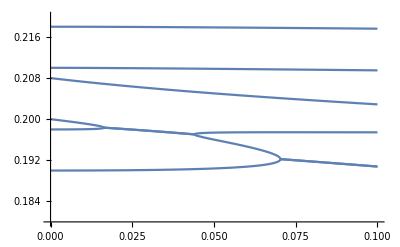
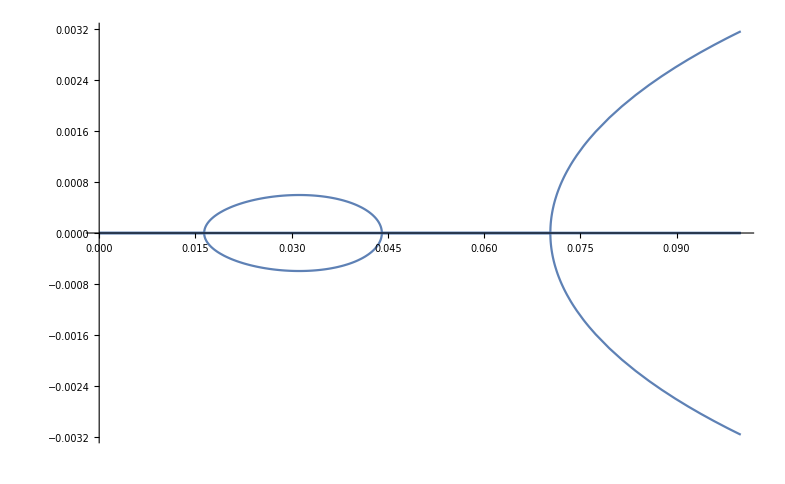

```mathematica
{Plot[Sort[Re[Eigenvalues[(M)/.{γ->π/4,cx->c .1,cy->c 0.0,ws->0.01,η->.008,νa->0.2}]]],{c,0,.1},PlotRange->{0.18,0.22}],Plot[Sort[Im[Eigenvalues[(M)/.{γ->π/4,cx->c .1,cy->c 0.0,ws->0.01,η->.008,νa->0.2}]]],{c,0,.1},PlotRange->All]}
```

```mathematica
eq=Simplify[(Det[(M/.{η->ws-δ})-(νa+Δ) IdentityMatrix[6]])/.{δ->δ ws,Δ->Δ ws}];
serδ=Normal[Series[eq,{δ,0,1}]];
serc=Normal[Series[(serδ/.{cx->c 0.1,cy->c 0,γ->π/4})/.{c->c ws},{c,0,1}]]
```

-2 ws^6 δ Δ-2 ws^6 Δ^2+6 ws^6 δ Δ^2+3 ws^6 Δ^3-ws^6 δ Δ^3+ws^6 Δ^4-6 ws^6 δ Δ^4-3 ws^6 Δ^5+3 ws^6 δ Δ^5+ws^6 Δ^6+c (-0.15 ws^6 δ-0.15 ws^6 Δ+0.6 ws^6 δ Δ+0.375 ws^6 Δ^2-0.225 ws^6 δ Δ^2-0.6 ws^6 δ Δ^3-0.375 ws^6 Δ^4+0.375 ws^6 δ Δ^4+0.15 ws^6 Δ^5)

```mathematica
Simplify[(serc/.{δ->0.2})==0]
```

ws (c (-0.2-0.2 Δ+2.2 Δ^2-0.8 Δ^3-2. Δ^4+1. Δ^5)+Δ (-2.66667-5.33333 Δ+18.6667 Δ^2-1.33333 Δ^3-16. Δ^4+6.66667 Δ^5))==0

```mathematica
d=Simplify[Solve[(((eq/.{cx->c 0.1,cy->c 0,γ->π/4})/.{c->c ws})/.{δ->0.2})==0,Δ]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Δ→Root[-276480 c+7840 c^2+480 c^3+(-3686400-537600 c+87808 c^2-816 c^3-4 c^4) #1+(-11776000+4116480 c-56000 c^2-1440 c^3+5 c^4) #1^2+(34406400-1382400 c-134400 c^2+1200 c^3) #1^3+(-1024000-3840000 c+84000 c^2) #1^4+(-30720000+1920000 c) #1^5+12800000 #1^6&,1]},{Δ→Root[-276480 c+7840 c^2+480 c^3+(-3686400-537600 c+87808 c^2-816 c^3-4 c^4) #1+(-11776000+4116480 c-56000 c^2-1440 c^3+5 c^4) #1^2+(34406400-1382400 c-134400 c^2+1200 c^3) #1^3+(-1024000-3840000 c+84000 c^2) #1^4+(-30720000+1920000 c) #1^5+12800000 #1^6&,2]},{Δ→Root[-276480 c+7840 c^2+480 c^3+(-3686400-537600 c+87808 c^2-816 c^3-4 c^4) #1+(-11776000+4116480 c-56000 c^2-1440 c^3+5 c^4) #1^2+(34406400-1382400 c-134400 c^2+1200 c^3) #1^3+(-1024000-3840000 c+84000 c^2) #1^4+(-30720000+1920000 c) #1^5+12800000 #1^6&,3]},{Δ→Root[-276480 c+7840 c^2+480 c^3+(-3686400-537600 c+87808 c^2-816 c^3-4 c^4) #1+(-11776000+4116480 c-56000 c^2-1440 c^3+5 c^4) #1^2+(34406400-1382400 c-134400 c^2+1200 c^3) #1^3+(-1024000-3840000 c+84000 c^2) #1^4+(-30720000+1920000 c) #1^5+12800000 #1^6&,4]},{Δ→Root[-276480 c+7840 c^2+480 c^3+(-3686400-537600 c+87808 c^2-816 c^3-4 c^4) #1+(-11776000+4116480 c-56000 c^2-1440 c^3+5 c^4) #1^2+(34406400-1382400 c-134400 c^2+1200 c^3) #1^3+(-1024000-3840000 c+84000 c^2) #1^4+(-30720000+1920000 c) #1^5+12800000 #1^6&,5]},{Δ→Root[-276480 c+7840 c^2+480 c^3+(-3686400-537600 c+87808 c^2-816 c^3-4 c^4) #1+(-11776000+4116480 c-56000 c^2-1440 c^3+5 c^4) #1^2+(34406400-1382400 c-134400 c^2+1200 c^3) #1^3+(-1024000-3840000 c+84000 c^2) #1^4+(-30720000+1920000 c) #1^5+12800000 #1^6&,6]}}

```mathematica
cs=Solve[3 c (cx1+cy1) (ws-4 δ)+4 ws δ+3 c (cx1-cy1) (ws-2 δ) Cos[2 γ]==0,c]
```

{{c→-(4 ws δ)/(3 (cx1 ws+cy1 ws-4 cx1 δ-4 cy1 δ+cx1 ws Cos[2 γ]-cy1 ws Cos[2 γ]-2 cx1 δ Cos[2 γ]+2 cy1 δ Cos[2 γ]))}}

```mathematica
(c/.cs)/.{γ->π/4,cx1->.1,cy1->0.2,ws->0.01,η->.008,νa->0.2,δ->0.002}
```

{-0.0444444}

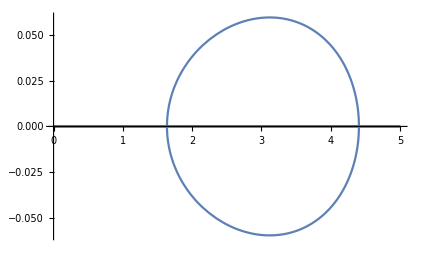

```mathematica
Plot[Im[(Δ/.d)/.{δ->0.2}],{c,0,5},PlotRange->All]
```

```mathematica
eq=Simplify[Det[(M/.{η->ws+δ,cx->c,cy->0,γ->0})-(νa+Δ) IdentityMatrix[6]]];
ser=Normal[Series[eq/.{c->(2 ws δ)/(3 (ws+3 δ))+x},{Δ,0,2}]]
serδ=Simplify[Normal[Series[Normal[Series[ser,{δ,0,1}]],{x,0,2}]]]
```

1/64 (96 ws^2 δ (2 ws^2+3 ws δ+δ^2) (x+(2 ws δ)/(3 (ws+3 δ)))-4 (2 ws^4-14 ws^3 δ-7 ws^2 δ^2) (x+(2 ws δ)/(3 (ws+3 δ)))^2)+1/64 (128 ws^4 δ+192 ws^3 δ^2+64 ws^2 δ^3-(32 ws^2 (3 ws x+2 ws δ+9 x δ) (2 ws^2+6 ws δ+3 δ^2))/(ws+3 δ)-4 (14 ws^3+30 ws^2 δ+24 ws δ^2+8 δ^3) (x+(2 ws δ)/(3 (ws+3 δ)))^2-12 δ (2 ws+δ) (x+(2 ws δ)/(3 (ws+3 δ)))^3+(-ws-δ) (x+(2 ws δ)/(3 (ws+3 δ)))^4) Δ+1/64 (-128 ws^4-384 ws^3 δ-192 ws^2 δ^2+(32 (3 ws x+2 ws δ+9 x δ) (3 ws^3+ws^2 δ-3 ws δ^2-δ^3))/(ws+3 δ)-4 (-25 ws^2-38 ws δ-19 δ^2) (x+(2 ws δ)/(3 (ws+3 δ)))^2-12 (-2 ws-2 δ) (x+(2 ws δ)/(3 (ws+3 δ)))^3+(x+(2 ws δ)/(3 (ws+3 δ)))^4) Δ^2

-2 ws^4 Δ^2-3 ws^3 δ Δ^2-1/16 ws x^2 (2 ws^3-14 ws^2 (δ-Δ)+5 ws (6 δ-5 Δ) Δ-50 δ Δ^2)+1/12 ws^2 x (ws^2 (34 δ-36 Δ)+43 δ Δ^2+2 ws Δ (-61 δ+27 Δ))

```mathematica
s=Solve[serδ==0,Δ]
```

{{Δ→(144 ws^3 x+42 ws^2 x^2+488 ws^2 x δ+90 ws x^2 δ-√((-144 ws^3 x-42 ws^2 x^2-488 ws^2 x δ-90 ws x^2 δ)^2-4 (-96 ws^3+216 ws^2 x+75 ws x^2-144 ws^2 δ+172 ws x δ+150 x^2 δ) (-6 ws^3 x^2+136 ws^3 x δ+42 ws^2 x^2 δ)))/(2 (-96 ws^3+216 ws^2 x+75 ws x^2-144 ws^2 δ+172 ws x δ+150 x^2 δ))},{Δ→(144 ws^3 x+42 ws^2 x^2+488 ws^2 x δ+90 ws x^2 δ+√((-144 ws^3 x-42 ws^2 x^2-488 ws^2 x δ-90 ws x^2 δ)^2-4 (-96 ws^3+216 ws^2 x+75 ws x^2-144 ws^2 δ+172 ws x δ+150 x^2 δ) (-6 ws^3 x^2+136 ws^3 x δ+42 ws^2 x^2 δ)))/(2 (-96 ws^3+216 ws^2 x+75 ws x^2-144 ws^2 δ+172 ws x δ+150 x^2 δ))}}

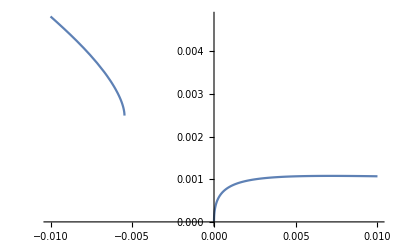

```mathematica
Plot[(Δ/.s[[1]])/.{ws->0.01,δ->0.002},{x,-.01,.01}]
```

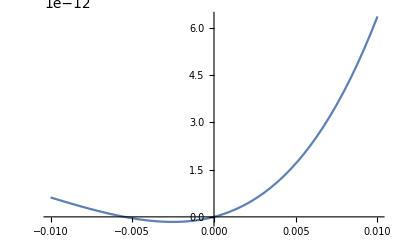

```mathematica
Plot[((-144 ws^3 x-42 ws^2 x^2-488 ws^2 x δ-90 ws x^2 δ)^2-4 (-96 ws^3+216 ws^2 x+75 ws x^2-144 ws^2 δ+172 ws x δ+150 x^2 δ) (-6 ws^3 x^2+136 ws^3 x δ+42 ws^2 x^2 δ))/.{ws->0.01,δ->0.002},{x,-.01,.01}]
```